## One Mode Approximation

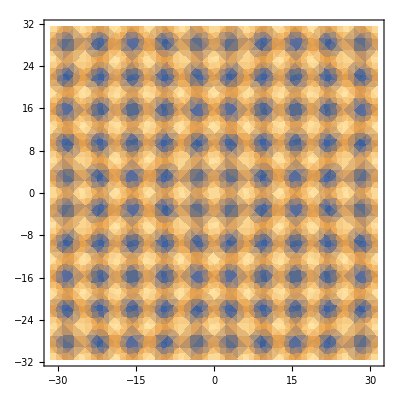

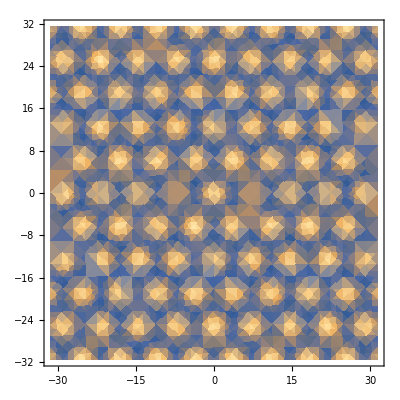

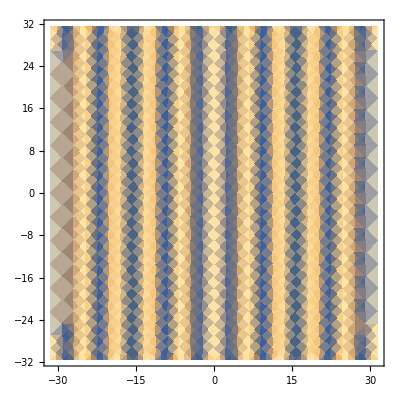

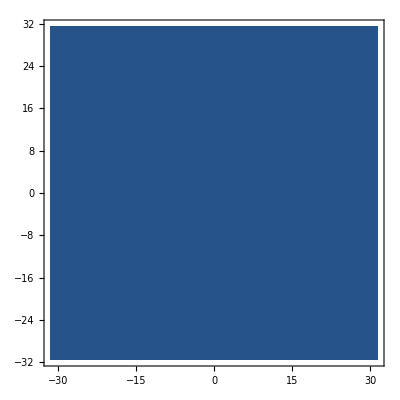

```mathematica
nsq[n_,A_,x_,y_]=n+A*(Cos[x]+Cos[y]);
ntr[n_,A_,x_,y_]=n+A*(Cos[(√3)/2 x]Cos[1/2 y]+1/2 Cos[y]);
nst[n_,A_,x_,y_]=n+A*(Cos[x]);
nlq[n_,A_,x_,y_]=n;
DensityPlot[nsq[0.0,1.0,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[ntr[0.0,1.0,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[nst[0.0,1.0,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[nlq[0.0,1.0,x,y],{x,-10π,10π},{y,-10π,10π}]
```

## The Kirkendall PFC Model

F(n)=∫n/2 Λn-t/3 n^3+v/4 n^4+γψ+ω/2 ψ^2+μ/4 ψ^4+κ/2∇ψ^2ⅆx
where  Λ=(B0l-B0x)+B2lψ^2+B0x(1+∇^2)^2

### The Integrand

```mathematica
gsq[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_,x_,y_]:=nsq[n,A,x,y]/2*((B0l-B0x)*nsq[n,A,x,y]+B2l*ψ^2*nsq[n,A,x,y]+B0x*(nsq[n,A,x,y]+2*Laplacian[nsq[n,A,x,y],{x,y}]+Laplacian[Laplacian[nsq[n,A,x,y],{x,y}],{x,y}]))-t/3*nsq[n,A,x,y]^3+v/4*nsq[n,A,x,y]^4+γ*ψ+ω/2*ψ^2+μ/4*ψ^4;
gtr[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_,x_,y_]:=ntr[n,A,x,y]/2*((B0l-B0x)*ntr[n,A,x,y]+B2l*ψ^2*ntr[n,A,x,y]+B0x*(ntr[n,A,x,y]+2*Laplacian[ntr[n,A,x,y],{x,y}]+Laplacian[Laplacian[ntr[n,A,x,y],{x,y}],{x,y}]))-t/3*ntr[n,A,x,y]^3+v/4*ntr[n,A,x,y]^4+γ*ψ+ω/2*ψ^2+μ/4*ψ^4;
gst[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_,x_,y_]:=nst[n,A,x,y]/2*((B0l-B0x)*nst[n,A,x,y]+B2l*ψ^2*nst[n,A,x,y]+B0x*(nst[n,A,x,y]+2*Laplacian[nst[n,A,x,y],{x,y}]+Laplacian[Laplacian[nst[n,A,x,y],{x,y}],{x,y}]))-t/3*nst[n,A,x,y]^3+v/4*nst[n,A,x,y]^4+γ*ψ+ω/2*ψ^2+μ/4*ψ^4;
glq[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_,x_,y_]:=nlq[n,A,x,y]/2*((B0l-B0x)*nlq[n,A,x,y]+B2l*ψ^2*nlq[n,A,x,y]+B0x*(nlq[n,A,x,y]+2*Laplacian[nlq[n,A,x,y],{x,y}]+Laplacian[Laplacian[nlq[n,A,x,y],{x,y}],{x,y}]))-t/3*nlq[n,A,x,y]^3+v/4*nlq[n,A,x,y]^4+γ*ψ+ω/2*ψ^2+μ/4*ψ^4;
```

### The Free Energy per Area (free energy density)

```mathematica
fsq[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=Integrate[Integrate[gsq[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ,x,y],{x,0,2π}],{y,0,2π}]/(4*π^2);
ftr[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=Integrate[Integrate[gtr[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ,x,y],{x,0,(4π)/(√3)}],{y,0,4π}]/((16* π^2)/(√3));
fst[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=Integrate[Integrate[gst[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ,x,y],{x,0,2π}],{y,0,1}]/(2π);
flq[n_,ψ_,A_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=Integrate[Integrate[glq[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ,x,y],{x,0,1}],{y,0,1}]/(1);
```

```mathematica
Solve[D[fsq[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ],A]==0,A]
Solve[D[ftr[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ],A]==0,A]
Solve[D[fst[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ],A]==0,A]
```

{{A→0},{A→-(2 √(-B0l+B0x+2 n t-3 n^2 v-B2l ψ^2))/(3 √v)},{A→(2 √(-B0l+B0x+2 n t-3 n^2 v-B2l ψ^2))/(3 √v)}}

{{A→0},{A→(4 (t-3 n v-√(t^2-15 B0l v+15 B0x v+24 n t v-36 n^2 v^2-15 B2l v ψ^2)))/(15 v)},{A→(4 (t-3 n v+√(t^2-15 B0l v+15 B0x v+24 n t v-36 n^2 v^2-15 B2l v ψ^2)))/(15 v)}}

{{A→0},{A→-(2 √(-B0l+B0x+2 n t-3 n^2 v-B2l ψ^2))/(√3 √v)},{A→(2 √(-B0l+B0x+2 n t-3 n^2 v-B2l ψ^2))/(√3 √v)}}

```mathematica
Asq[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=(2 √(-B0l+B0x+2 n t-3 n^2 v-B2l ψ^2))/(3 √v);
Atr[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=(4 (t-3 n v+√(t^2-15 B0l v+15 B0x v+24 n t v-36 n^2 v^2-15 B2l v ψ^2)))/(15 v);
Ast[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=(2 √(-B0l+B0x+2 n t-3 n^2 v-B2l ψ^2))/(√3 √v);
```

```mathematica
Fsq[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=fsq[n,ψ,Asq[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],B0l,B0x,B2l,t,v,γ,ω,μ];
Ftr[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=ftr[n,ψ,Atr[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],B0l,B0x,B2l,t,v,γ,ω,μ];
Fst[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=fst[n,ψ,Ast[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],B0l,B0x,B2l,t,v,γ,ω,μ];
Flq[n_,ψ_,B0l_,B0x_,B2l_,t_,v_,γ_,ω_,μ_]=flq[n,ψ,A,B0l,B0x,B2l,t,v,γ,ω,μ];
```

### The Phase Diagram

```mathematica
B0l=0.7;
B2l = -1.8;
B0x = 1.0;
t = 0.6;
v = 1.0;
γ = 0.0;
ω = 1.0;
μ = 4.0;
```

```mathematica
Manipulate[Plot[{Fsq[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],Ftr[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],Fst[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],Flq[n,ψ,B0l,B0x,B2l,t,v,γ,ω,μ]},{n,-0.5,0.5},PlotLegends->{"square","triangle","stripe","liquid"}],{ψ,-0.5,0.5}]
```

Noticed that the square free energy (blue) is always above the stripe free energy (green).

#### the common tangent line

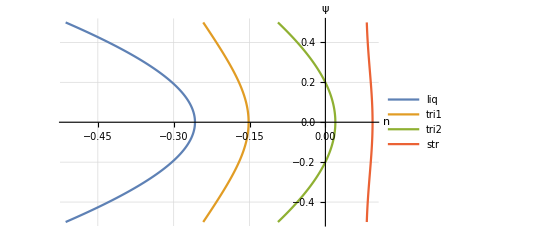

```mathematica
calPhad[ψ_]:={nlq, ntr1, ntr2, nst}/.Join[FindRoot[{D[Flq[nlq,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],nlq]==D[Ftr[ntr1,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],ntr1],D[Flq[nlq,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],nlq]==(Flq[nlq,ψ,B0l,B0x,B2l,t,v,γ,ω,μ]-Ftr[ntr1,ψ,B0l,B0x,B2l,t,v,γ,ω,μ])/(nlq-ntr1)},{nlq,-0.3},{ntr1,-0.1}],FindRoot[{D[Ftr[ntr2,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],ntr2]==D[Fst[nst,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],nst],D[Ftr[ntr2,ψ,B0l,B0x,B2l,t,v,γ,ω,μ],ntr2]==(Ftr[ntr2,ψ,B0l,B0x,B2l,t,v,γ,ω,μ]-Fst[nst,ψ,B0l,B0x,B2l,t,v,γ,ω,μ])/(ntr2-nst)},{ntr2,-0.1},{nst,0.1}]];
data = Transpose[calPhad[#]&/@Range[-0.5,0.5,.01]];
epsilon = Range[-0.5,0.5,.01];
ListLinePlot[Transpose[{#,epsilon}]&/@data,AxesLabel->{"n","ψ"}, PlotLegends->{"liq","tri1","tri2","str"},GridLines->Automatic]
```